```mathematica
f[x_]=exp(x-(x/4)^2)*th((x/11)^3+1/3);
```

```mathematica
a=0;b=6;n=10;h=(b-a)/n;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]]
```

{{0.,0.},{0.6,4.90438},{1.2,6.98267},{1.8,6.67339},{2.4,5.3485},{3.,3.90999},{3.6,2.82088},{4.2,2.26059},{4.8,2.21428},{5.4,2.53954},{6.,3.03234}}

```mathematica
p1=Fit[data,{1,x},x]
```

4.60587-0.302364 x

```mathematica
pr1[x_]=p1
```

4.60587-0.302364 x

```mathematica
gr6=Plot[pr1[x],{x,0,6},PlotStyle->Thickness[0.0056]];
```

```mathematica
gr1=Plot[f[x],{x,0,6},PlotStyle->Red];
```

```mathematica
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
```

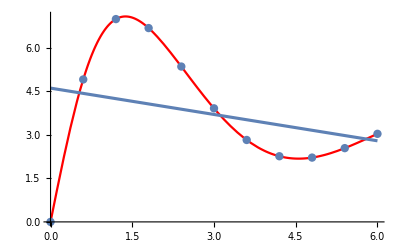

```mathematica
Show[gr1,gr2,gr6]
```

```mathematica
n=Length[data];
```

```mathematica
xValues=data[[All,1]];
```

```mathematica
yValues=data[[All,2]];
```

```mathematica
sumX=Total[xValues];
```

```mathematica
sumY=Total[yValues];
```

```mathematica
sumXY=Total[xValues*yValues];
```

```mathematica
sumX2=Total[xValues^2];
```

```mathematica
a1=(n*sumXY-sumX*sumY)/(n*sumX2-sumX^2);
```

```mathematica
a0=(sumY-a1*sumX)/n;
```

```mathematica
Q1[x_]:=a0+a1*x;
```

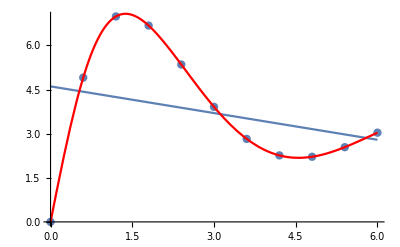

```mathematica
Show[ListPlot[data, PlotStyle->PointSize[0.015],PlotStyle->Blue],Plot[Q1[x],{x,0,6}],gr1]
```

```mathematica
dataf = Table[{data[[i, 1]], f[data[[i, 1]]]}, {i, Length[data]}];
```

```mathematica
n = Length[data];
```

```mathematica
A = Table[{1, data[[i, 1]], data[[i, 1]]^2}, {i, n}];
```

```mathematica
B = Table[data[[i, 2]], {i, n}];
```

```mathematica
sol = LinearSolve[Transpose[A].A, Transpose[A].B];
```

```mathematica
Q2[x_] := sol[[1]] + sol[[2]] x + sol[[3]] x^2;
```

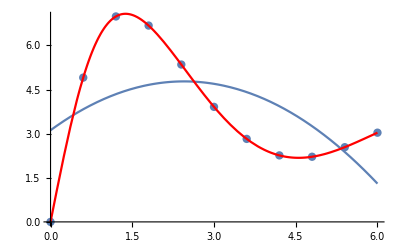

```mathematica
Show[ListPlot[data, PlotStyle->PointSize[0.015],PlotStyle->Blue], Plot[Q2[x], {x, 0, 6}],gr1]
```

```mathematica
p3=Fit[data,{1,x,x^2,x^3},x]
```

0.688835+7.77904 x-3.08417 x^2+0.31201 x^3

```mathematica
pr3[x_]=p3
```

0.688835+7.77904 x-3.08417 x^2+0.31201 x^3

```mathematica
gr7=Plot[pr3[x],{x,0,6},PlotStyle->Green];
```

```mathematica
p4=Fit[data,{1,x,x^2,x^3,x^4},x]
```

-0.0338439+11.9612 x-6.56931 x^2+1.24138 x^3-0.0774476 x^4

```mathematica
pr4[x_]=p4
```

-0.0338439+11.9612 x-6.56931 x^2+1.24138 x^3-0.0774476 x^4

```mathematica
gr8=Plot[pr4[x],{x,0,6},PlotStyle->Thickness[0.0056]];
```

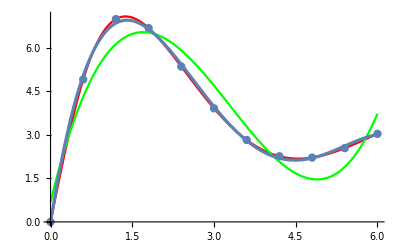

```mathematica
Show[gr1,gr2,gr7,gr8,Plot[Q2[x_],{x,0,6}],Plot[Q1[x_],{x,0,6}]]
```

```mathematica
Q1[2.4316]
```

3.87064

```mathematica
Q2[2.4316]
```

4.77535

```mathematica
pr3[2.4316]
```

5.85448

```mathematica
pr4[2.4316]
```

5.34892